```mathematica
By Le Chen.
Crated on Tue 31 May 2022 06:06:03 PM CDT
```

```mathematica
Integrate[√(2-ξ) Cos[ x ξ],{ξ,0,2},Assumptions->x>0]//FullSimplify
```

(√(π/2) (-Cos[2 x] FresnelS[(2 √x)/(√π)]+FresnelC[(2 √x)/(√π)] Sin[2 x]))/x^(3/2)

```mathematica
Limit[(√(π/2) (-Cos[2 x] FresnelS[(2 √x)/(√π)]+FresnelC[(2 √x)/(√π)] Sin[2 x]))/x^(3/2),x->0]
```

(4 √2)/3

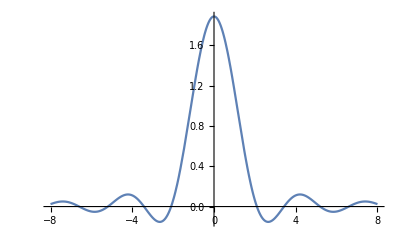

```mathematica
Plot[(√(π/2) (-Cos[2 x] FresnelS[(2 √x)/(√π)]+FresnelC[(2 √x)/(√π)] Sin[2 x]))/x^(3/2),{x,-8,8}]
```

```mathematica
Data=Table[{x,(√(π/2) (-Cos[2 x] FresnelS[(2 √Abs[x])/(√π)]+FresnelC[(2 √Abs[x])/(√π)] Sin[2Abs[ x]]))/Abs[x]^(3/2)},{x,-8.001,8.001,0.1}];

Export["InverseFourier.csv",PrependTo[Data,{x,y}],"CSV"]
```

InverseFourier.csv